```mathematica
ldos=Import[NotebookDirectory[]<>"ldos_e"<>ToString[#]<>".dat"]&/@(Range[-3.*10^-3,7.*10^-3,10^-4]/.{0.->0});
```

```mathematica
Max[ldos]
```

278.632

```mathematica
Log@(Max[ldos]+1)
```

5.63347

```mathematica
fig2=ArrayPlot[Reverse@#,ColorFunction->(ColorData["GrayTones"][1-#/280]&),ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{Automatic,{0,280}},LegendLabel->"LDOS"],Left],PlotRangePadding->None]&/@(ldos);
```

```mathematica
fig3=ArrayPlot[Log[Reverse@#+1],ColorFunction->(ColorData["GrayTones"][1-#/5.7]&),ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{Automatic,{0,5.7}},LegendLabel->"ln(LDOS+1)"],Left],PlotRangePadding->None]&/@(ldos);
```

```mathematica
dos=Total[ldos,{2,3}];
```

```mathematica
energylist=Subdivide[-3,7,100];
```

```mathematica
dosfig=Table[ListLinePlot[dos,Frame->True,DataRange->{-3,7},Axes->False,Epilog->{ {PointSize[Large],Point[{energylist[[i]],dos[[i]]}]},Line[{{energylist[[i]],0},{energylist[[i]],300000}}]},PlotLabel->"DOS="<>ToString[dos[[i]]],ImageSize->{Automatic,200}],{i,1,101}];
```

```mathematica
enfig=Import["D:\\QuS\\Kagome_matlab\\data\\fig\\545\\mgk"<>ToString[#]<>".png"]&/@(Range[-3.*10^-3,7.*10^-3,10^-4]/.{0.->0});
```

```mathematica
ft=MapThread[Grid[{{#1,#2,#3,Pane[#4,{Automatic,250}]}},Spacings->{0,0,0}]&,{fig2,fig3,dosfig,enfig}];
```

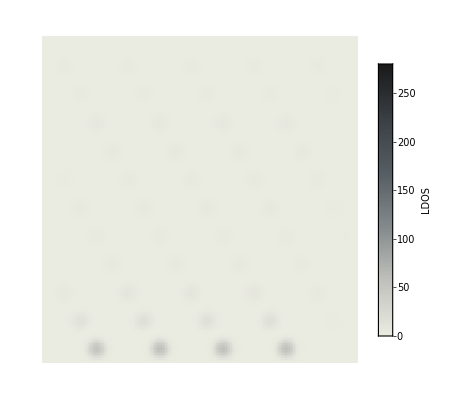
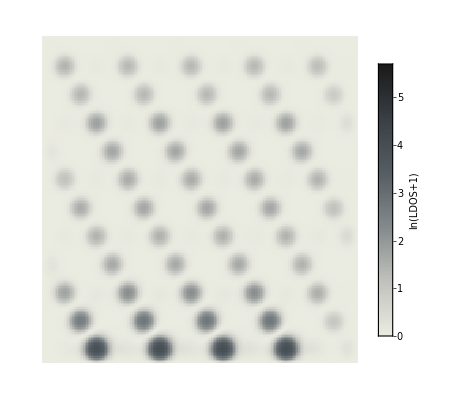
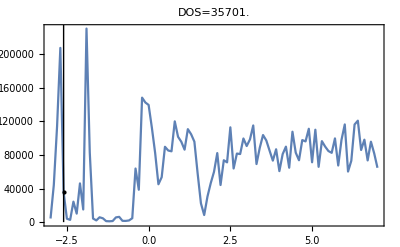
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ft[[5]]
```

```mathematica
Export["545.avi",ft,"FrameRate"->4]//AbsoluteTiming
```

{54.2201,545.avi}